Disclaimer: This is not the code used to generate the plots in our paper. It is provided solely for illustrative purposes, to demonstrate how to use the data and for testing.

```mathematica
path=NotebookDirectory[];
```

## Fig 1

```mathematica
data=Import[path<>"fig_1_decay_data.csv"];
numericData=ToExpression/@Rest[data];
```

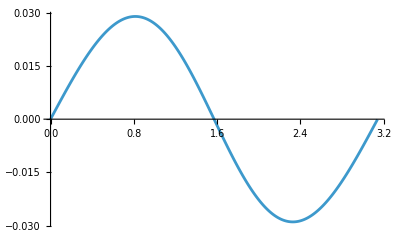

```mathematica
{Transpose[numericData][[1]],Transpose[numericData][[4]]}//Transpose//ListLinePlot
```

```mathematica
data=Import[path<>"fig_1_inset.csv"];
numericData=ToExpression/@Rest[data];
```

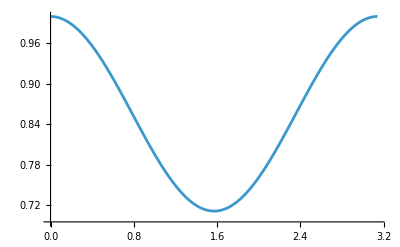

```mathematica
{Transpose[numericData][[1]],Transpose[numericData][[3]]}//Transpose//ListLinePlot
```

## Fig 2

```mathematica
data=Import[path<>"fig_2_and_3_evol_data.csv"];
numericData=ToExpression/@Rest[data];
```

```mathematica
data
```

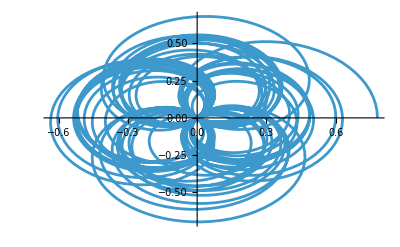

```mathematica
{Transpose[numericData][[2]],Transpose[numericData][[3]]}//Transpose//ListLinePlot
```

## Fig 3

## Fig 4

```mathematica
data=Import[path<>"fig_4_ising_data.csv"];data=Rest[data]//ToExpression;
```

```mathematica
Partition[Map[{#[[1]],#[[2]],ListSurfacePlot3D[#[[3]]]}&,data],4]//TableForm//Rasterize
```

-Graphics-

## Fig 5

```mathematica
data=Import[path<>"fig_5_convergence.csv"];
numericData=ToExpression/@Rest[data];
```

```mathematica
data
```

{{g,curve},{0.1,{{5, 0.0017139883677191445}, {6, 0.00010816835090895383}, {7, 4.304133087646926*^-6}, {8, 1.1704413659978235*^-7}, {9, 2.3052235426089468*^-9}, {10, 3.434623263271577*^-11}}},{0.5,{{5, 0.03475386176070017}, {6, 0.010148467996165884}, {7, 0.0019945991991614917}, {8, 0.0002743982460845091}, {9, 0.000027572237332799904}, {10, 2.0980834000134837*^-6}}},{1.,{{5, 0.059388303323570917}, {6, 0.029099078216220292}, {7, 0.012198627134378191}, {8, 0.003673547827671765}, {9, 0.0008051674378343046}, {10, 0.00013219225602411266}}},{1.5,{{5, 0.043388752292281965}, {6, 0.021614317340897575}, {7, 0.010806181559680515}, {8, 0.004922516465965309}, {9, 0.001987842039641068}, {10, 0.0005907040612160559}}}}

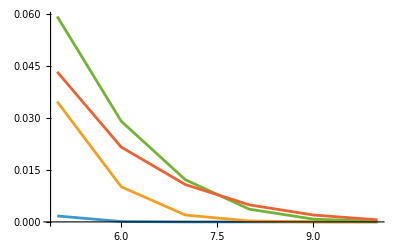

```mathematica
numericData[[All,2]]//ListLinePlot
```

```mathematica
data=Import[path<>"/fig_5_inset_convergence.csv"];
```

```mathematica
data=Rest[data]//ToExpression
```

{{0.1,{{9,2.30522×10^-9},{10,2.30272×10^-9}}},{0.5,{{9,0.0000275722},{10,0.0000273526}}},{1.,{{9,0.000805167},{10,0.000787289}}},{1.5,{{9,0.00198784},{10,0.00185221}}}}

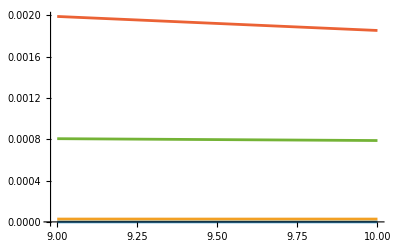

```mathematica
data[[All,2]]//ListLinePlot
```